{{0.0232831,0.478781},{0.478781,0.794887},{0.794887,0.0535114},{0.0535114,0.258862},{0.258862,0.160853},{0.160853,0.33045},{0.33045,0.571551},{0.571551,0.818533},7821,{0.790019,0.127518},{0.127518,0.653425},{0.653425,0.207603},{0.207603,0.0768558},{0.0768558,0.710389},{0.451711,0.075003},{0.075003,0.59724}}
 |  |  |  |

{{0.818533,0.849332},{0.849332,0.936758},{0.936758,0.631268},{0.950771,0.94032},{0.94032,0.93603},{0.93603,0.466762},{0.433431,0.97209},{0.97209,0.261247},2148,{0.707596,0.884284},{0.884284,0.693508},{0.785519,0.969853},{0.969853,0.963693},{0.963693,0.48409},{0.710389,0.890455},{0.890455,0.992384},{0.992384,0.451711}}
 |  |  |  |

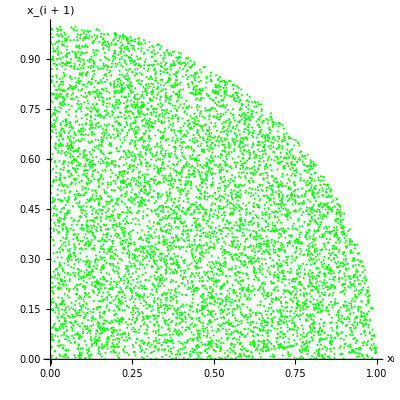

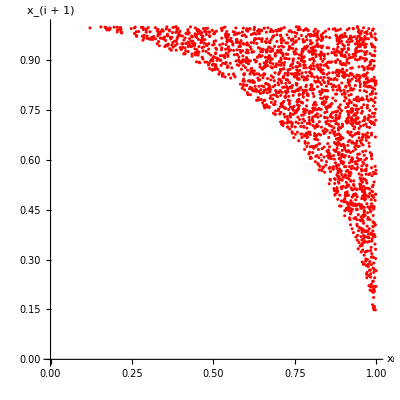

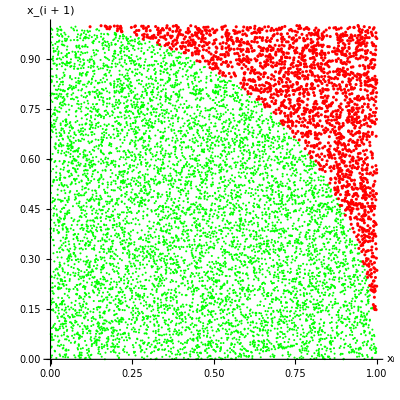

/home/parada/college/fc/Projeto1/dentrofora3.pdf

```mathematica
dados = Import["/home/parada/college/fc/Projeto1/dentro.txt","Table"]
dados2 = Import["/home/parada/college/fc/Projeto1/fora.txt","Table"]
fig = ListPlot[dados, AxesLabel->{"x_i","x_(i + 1)"},  PlotStyle->Green, AspectRatio->1]
fig2 = ListPlot[dados2, AxesLabel->{"x_i","x_(i + 1)"},  PlotStyle->Red, AspectRatio->1]
Show[fig,fig2]

Export["/home/parada/college/fc/Projeto1/dentrofora3.pdf", Show[fig,fig2],"PDF"]
```